```mathematica
(*Start more fancy method???*)
r0={1,0};
r1={0,1};
Lx=16;
Ly=16;
J=1;
l=Flatten[Table[x*r0+y*r1,{y,0,Ly-1},{x,0,Lx-1}],1];
(*non-periodic*)
Bonds=DeleteCases[Flatten[Table[If[i<j&&Norm[l[[i]]-l[[j]]]==1,{i,j},"a"],{i,1,Length[l]},{j,1,Length[l]}],1],_String];
ϕlist=Flatten[Table[{ToExpression["ϕ"<>ToString[i]]},{i,1,Lx*Ly}]];
θlist=Flatten[Table[{ToExpression["θ"<>ToString[i]]},{i,1,Lx*Ly}]];
dBonds=Table[If[(l⟦Bonds⟦i,2⟧⟧-l⟦Bonds⟦i,1⟧⟧)⟦1⟧≠0&&l⟦Bonds⟦i,1⟧⟧⟦1⟧≥0,{ 0,-dx,0},{dy,0,0}],{i,1,Length[Bonds]}];
(*Kugelkoordinaten*)
S[ϕ_,θ_]:={Cos[ϕ]Sin[θ],Sin[ϕ]Sin[θ],Cos[θ]};
Neelstatearglist=Flatten[{Table[{ϕlist⟦i⟧,0},{i,1,Lx*Ly}],
Table[{θlist⟦i⟧,(1-(-1)^i)*π/2},{i,1,Lx*Ly}]},1];
```

```mathematica
Hnew=Sum[J*(S[ϕlist⟦Bonds⟦i,1⟧⟧,θlist⟦Bonds⟦i,1⟧⟧].S[ϕlist⟦Bonds⟦i,2⟧⟧,θlist⟦Bonds⟦i,2⟧⟧])+
dBonds⟦i⟧.(Cross[S[ϕlist⟦Bonds⟦i,1⟧⟧,θlist⟦Bonds⟦i,1⟧⟧],S[ϕlist⟦Bonds⟦i,2⟧⟧,θlist⟦Bonds⟦i,2⟧⟧]]),{i,1,Length[Bonds]}];
```

```mathematica
tingeldangelbob=Module[{dd,step=0.01,dangle={},MinArgList=Neelstatearglist},
For[dd=0.00,dd≤0.2,dd=dd+step,
(*MinArgList=FindMinimum[{Hnew/.{dx->dd,dy->dd+step},And@@Flatten[{Table[ϕlist⟦i⟧>-π && ϕlist⟦i⟧≤π,{i,Length[ϕlist]}],Table[θlist⟦i⟧>0 && θlist⟦i⟧≤π,{i,Length[θlist]}]}]},MinArgList]⟦2⟧/.Rule->List;*)
MinArgList=FindMinimum[{Hnew/.{dx->dd,dy->dd},And@@Flatten[{Table[ϕlist⟦i⟧>-π && ϕlist⟦i⟧≤π,{i,Length[ϕlist]}],Table[θlist⟦i⟧>0 && θlist⟦i⟧≤π,{i,Length[θlist]}]}]},MinArgList]⟦2⟧/.Rule->List;
(*MinArgList=FindMinimum[Hnew/.{dx->dd+step,dy->dd},MinArgList,Method->"PrincipalAxis"]⟦2⟧/.Rule->List;
MinArgList=FindMinimum[Hnew/.{dx->dd+step,dy->dd+step},MinArgList,Method->"PrincipalAxis"]⟦2⟧/.Rule->List;*)
AppendTo[dangle,Flatten[{dd,Transpose[MinArgList][[2]]}]];
];
dangle
];
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

```mathematica
θarray=ArrayReshape[tingeldangelbob[[-1,Lx*Ly+2;;-1]],{Ly,Lx}];
ϕarray=ArrayReshape[tingeldangelbob[[-1,2;;Lx*Ly+1]],{Ly,Lx}];
Grid[{{ArrayPlot[ϕarray,PlotLegends->Automatic,Mesh->True,ColorFunction->"Rainbow"],ArrayPlot[θarray,PlotLegends->Automatic,Mesh->True,ColorFunction->"Rainbow"],ArrayPlot[Chop[Differences[ϕarray]],PlotLegends->Automatic,Mesh->True,ColorFunction->"Rainbow"],,ArrayPlot[Chop[Differences[θarray]],PlotLegends->Automatic,Mesh->True,ColorFunction->"Rainbow"]}}]
```

-Graphics- | -Graphics- | -Graphics- |  | -Graphics-

```mathematica
textureplot[arglist_]:=Graphics3D[{PointSize[0.01],Point[Flatten[Table[Table[{i,j,0},{i,0,Lx-1}],{j,0,Lx-1}],1]],Table[Arrow[Tube[{{i,j,0},{i,j,0}+1*S[arglist[[i*Ly+j+1]],arglist[[i*Ly+j+1+Lx*Ly]]]}]],{i,0,Lx-1},{j,0,Ly-1}]}];
```

```mathematica
textureplot[tingeldangelbob[[-1,2;;]]]
```

-Graphics3D-

```mathematica
n=0;
Table[l[[y*Lx+1+n]],{y,0,Ly-1}]
Table[l[[n*Ly+x]],{x,1,Lx}]
```

{{0,0},{0,1},{0,2},{0,3}}

{{0,0},{1,0},{2,0},{3,0}}

```mathematica
Table[l[[(y)*Lx+1+x]],{y,0,Ly-1},{x,0,Lx-1}]
```

{{{0,0},{1,0},{2,0},{3,0}},{{0,1},{1,1},{2,1},{3,1}},{{0,2},{1,2},{2,2},{3,2}},{{0,3},{1,3},{2,3},{3,3}}}

```mathematica
ϕplotlist=tingeldangelbob⟦-1,2;;Lx*Ly+1⟧;
θplotlist=tingeldangelbob⟦-1,Lx*Ly+2;;2Lx*Ly+1⟧;
(*ϕplotlist=Neelstatearglist[[1;;Lx*Ly,2]];
θplotlist=Neelstatearglist[[Lx*Ly+1;;2*Lx*Ly,2]];*)
help=Table[Flatten[Table[{{0.2,0,0}.Cross[S[ϕplotlist⟦y*Lx+1+x⟧,θplotlist⟦y*Lx+1+x⟧],S[ϕplotlist⟦(y+1)*Lx+1+x⟧,θplotlist⟦(y+1)*Lx+1+x⟧]]},{y,0,Ly-2}]],{x,0,Lx-1}];
testlisty=Table[Flatten[Table[{help[[i]][[j]],0},{i,1,Ly-1}]],{j,1,Lx-1}];
testlistx=Table[Flatten[Table[{0,{0,-0.2,0}.Cross[S[ϕplotlist⟦y*Lx+1+x⟧,θplotlist⟦y*Lx+1+x⟧],S[ϕplotlist⟦(y)*Lx+x+2⟧,θplotlist⟦(y)*Lx+x+2⟧]]},{x,0,Lx-2}]],{y,0,Ly-1}];
testlist3=Table[{testlistx[[i]],testlisty[[i]]},{i,1,Length[testlistx]-1}];
MatrixPlot[testlistx,PlotLegends->Automatic]
MatrixPlot[testlisty,PlotLegends->Automatic]
MatrixPlot[Flatten[testlist3,1],PlotLegends->Automatic]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Clear[bklist]
bklist[κ_]:=Flatten[{dx->tingeldangelbob[[κ,1]],Table[Flatten[{ϕlist,θlist}]⟦i⟧->tingeldangelbob[[κ,2;;]]⟦i⟧,{i,1,2Lx*Ly}]}];
dy=0.2;
xspiralstate=Flatten[{{dx->0.2},Table[{ϕlist⟦i⟧->0},{i,1,Lx*Ly}],
Table[{θlist⟦i⟧->l⟦i⟧⟦1⟧*ArcTan[dy]+0*l⟦i⟧⟦2⟧*ArcTan[dy]},{i,1,Lx*Ly}]}];
```

```mathematica
Hnew/.xspiralstate
```

23.2963

```mathematica
Hnew/.bklist[-1]
Hnew/.bklist[1]
```

-485.726

-384.

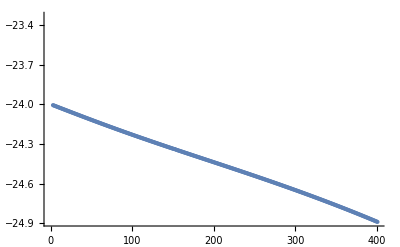

```mathematica
ListPlot[Table[Hnew/.bklist[s],{s,1,Length[tingeldangelbob]}]]
```

```mathematica
Hnew/.bklist[Length[tingeldangelbob]]
```

Cos[θ1000] Cos[θ1001]+Cos[θ1001] Cos[θ1002]+Cos[θ1002] Cos[θ1003]+Cos[θ1003] Cos[θ1004]+Cos[θ1004] Cos[θ1005]+Cos[θ1005] Cos[θ1006]+Cos[θ1006] Cos[θ1007]+Cos[θ1007] Cos[θ1008]+Cos[θ1008] Cos[θ1009]+Cos[θ100] Cos[θ101]+8940+Sin[θ996] Sin[θ997] Sin[ϕ996] Sin[ϕ997]+0.2 (Cos[θ997] Sin[θ965] Sin[ϕ965]-Cos[θ965] Sin[θ997] Sin[ϕ997])+Sin[θ966] Sin[θ998] Sin[ϕ966] Sin[ϕ998]+Sin[θ997] Sin[θ998] Sin[ϕ997] Sin[ϕ998]+0.2 (Cos[θ998] Sin[θ966] Sin[ϕ966]-Cos[θ966] Sin[θ998] Sin[ϕ998])+Sin[θ1000] Sin[θ999] Sin[ϕ1000] Sin[ϕ999]+Sin[θ967] Sin[θ999] Sin[ϕ967] Sin[ϕ999]+Sin[θ998] Sin[θ999] Sin[ϕ998] Sin[ϕ999]+0.2 (Cos[θ999] Sin[θ967] Sin[ϕ967]-Cos[θ967] Sin[θ999] Sin[ϕ999])
 |  |  |  |

```mathematica
energydimlist={{6,6,-61.05555394924338},{4,4,-24.4402717784584},{8,8,-113.73689770841767},{10,10,-182.38882635505993},{12,12,-267.3598190692088},{14,14,-368.5767116763112},{16,16,-485.72632301175025},{18,18,-619.025472659022},{20,20,-769.0483143590886},{22,22,-934.760300729925},{24,24,-1116.5111266724389},{32,32,-2003.612660646481}};
```

```mathematica
bklist[κ_]:=Flatten[{dx->tingeldangelbob[[κ,1]],Table[Flatten[{ϕlist,θlist}]⟦i⟧->tingeldangelbob[[κ,2;;]]⟦i⟧,{i,1,2Lx*Ly}]}];
AppendTo[energydimlist,{Lx,Ly,(Hnew/.bklist[Length[tingeldangelbob]])}]
```

{{6,6,-61.0556},{4,4,-24.4403},{8,8,-113.737},{10,10,-182.389},{12,12,-267.36},{14,14,-368.577},{16,16,-485.726},{18,18,-619.025},{20,20,-769.048},{22,22,-934.76},{24,24,-1116.51},{32,32,-2003.61}}

```mathematica
(*spin chirality*)
x=0;
y=0;
ϕplotlist=tingeldangelbob⟦-1,2;;Lx*Ly+1⟧;
θplotlist=tingeldangelbob⟦-1,Lx*Ly+2;;2Lx*Ly+1⟧;
chirallist=Table[S[ϕplotlist⟦(y)*Lx+1+x⟧,θplotlist⟦(y)*Lx+1+x⟧].Cross[S[ϕplotlist⟦(y+1)*Lx+1+x⟧,θplotlist⟦(y+1)*Lx+1+x⟧],S[ϕplotlist⟦(y)*Lx+1+x+1⟧,θplotlist⟦(y)*Lx+1+x+1⟧]],{x,0,Lx-2},{y,0,Ly-2}];
```

```mathematica
MatrixPlot[chirallist,PlotLegends->Automatic]
```

-Graphics-

```mathematica
Sum[chirallist[[i]][[j]],{i,1,Lx-1},{j,1,Ly-1}]
Sum[(-1)^(i+j)*chirallist[[i]][[j]],{i,1,Lx-1},{j,1,Ly-1}]
```

0.12193

-0.472838

```mathematica
Lx=16;
Ly=16;
dx=0.30;
l=Flatten[Table[x*r0+y*r1,{y,0,Ly-1},{x,0,Lx-1}],1];
spiraltlist=Table[Modulo[(1-(-1)^(l⟦i⟧⟦2⟧+1))*π/2-1*l⟦i⟧⟦1⟧*ArcTan[dx]+0*l⟦i⟧⟦2⟧*ArcTan[dx]],{i,1,Lx*Ly}];
spiralplist=Table[0,{i,1,Lx*Ly}];
alist=Flatten[{spiralplist,spiraltlist}];
```

```mathematica
x=6;
textureplot[arglist_]:=Graphics3D[{PointSize[0.01],Point[Flatten[Table[Table[{i,j,0},{i,0,Lx-1}],{j,x,x}],1]],Table[Arrow[Tube[{{i,j,0},{i,j,0}+1*S[arglist[[i*Ly+j+1]],arglist[[i*Ly+j+1+Lx*Ly]]]}]],{i,0,Lx-1},{j,x,x}]}];
spiraltlist=Table[Modulo[π+l[[i]][[2]]*ArcTan[dx]],{i,1,Lx*Ly}];
spiralplist=Table[0,{i,1,Lx*Ly}];
alist=Flatten[{spiralplist,spiraltlist}];
textureplot[alist]
```

-Graphics3D-

```mathematica
textureplot[arglist_]:=Graphics3D[{PointSize[0.01],Point[Flatten[Table[Table[{i,j,0},{i,0,Lx-1}],{j,0,Lx-1}],1]],Table[Arrow[Tube[{{i,j,0},{i,j,0}+1*S[arglist[[i*Ly+j+1]],arglist[[i*Ly+j+1+Lx*Ly]]]}]],{i,0,Lx-1},{j,0,Ly-1}]}];
spiraltlist=Table[π+l[[i]][[2]]*ArcTan[dx]+If[Mod[Total[l[[i]]],2]==0,π,0],{i,1,Lx*Ly}];
spiraltlist=Table[l[[i]][[2]]*ArcTan[dx]+3π/2-π/2(-1)^(Total[l[[i]]]),{i,1,Lx*Ly}];
spiralplist=Table[0,{i,1,Lx*Ly}];
alist=Flatten[{spiralplist,spiraltlist}];
textureplot[alist]
```

-Graphics3D-

```mathematica
dx=0.3;
xspiraltlist=Table[(1-(-1)^(l⟦i⟧⟦1⟧+l⟦i⟧⟦2⟧))*π/2-1*l⟦i⟧⟦1⟧*ArcTan[dx]+0*l⟦i⟧⟦2⟧*ArcTan[dx],{i,1,Lx*Ly}];
yspiraltlist=Table[(1-(-1)^(l⟦i⟧⟦1⟧+l⟦i⟧⟦2⟧))*π/2-0*l⟦i⟧⟦1⟧*ArcTan[dx]+1*l⟦i⟧⟦2⟧*ArcTan[dx],{i,1,Lx*Ly}];
alist=Flatten[{spiralplist,yspiraltlist}];
```

```mathematica
NikOffset=Lx/2;
NikList=Flatten[{alist[[1+NikOffset;;;;Lx]],alist[[Lx*Ly+1+NikOffset;;;;Lx]]}]
TeXNiklas[Liste_]:=Graphics3D[{PointSize[0.01],Point[Table[{i,0,-2*Mod[i,2]},{i,0,Lx-1}]],Table[Arrow[Tube[{{i,0,-2*Mod[i,2]},{i,0,-2*Mod[i,2]}+1*S[Liste[[i+1]],Liste[[i+1+Lx]]]}]],{i,0,Lx-1}]}];
TeXNiklas[Liste_]:=Graphics3D[{PointSize[0.01],Point[Table[{i,0,-0*Mod[i,2]},{i,0,Lx-1}]],Table[Arrow[Tube[{{i,0,-0*Mod[i,2]},{i,0,-0*Mod[i,2]}+1*S[Liste[[i+1]],Liste[[i+1+Lx]]]}]],{i,0,Lx-1}]}];
TeXNiklas[NikList]
NikList/π
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,3.43305,0.582914,4.01596,1.16583,4.59888,1.74874,5.18179,2.33165,5.7647,2.91457,6.34762,3.49748,6.93053,4.0804,7.51344,0.,3.43305,0.582914,4.01596,1.16583,4.59888,1.74874,5.18179,2.33165,5.7647,2.91457,6.34762,3.49748,6.93053,4.0804,7.51344}

-Graphics3D-

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,1.09277,0.185547,1.27832,0.371094,1.46387,0.556641,1.64942,0.742189,1.83496,0.927736,2.02051,1.11328,2.20606,1.29883,2.3916,0.,1.09277,0.185547,1.27832,0.371094,1.46387,0.556641,1.64942,0.742189,1.83496,0.927736,2.02051,1.11328,2.20606,1.29883,2.3916}

-Graphics3D-

```mathematica
Lx=16;
Ly=16;
d=30;
x=6;
textureplot[arglist_]:=Graphics3D[{PointSize[0.01],Point[Flatten[Table[Table[{i,j,0},{i,x,x}],{j,0,Ly-1}],1]],Table[Arrow[Tube[{{i,j,0},{i,j,0}+1*S[arglist[[i*Ly+j+1]],arglist[[i*Ly+j+1+Lx*Ly]]]}]],{i,x,x},{j,0,Ly-1}]}];
textureplot[arglist_]:=Graphics3D[{PointSize[0.01],Point[Flatten[Table[Table[{i,j,0},{i,0,Lx-1}],{j,0,Lx-1}],1]],Table[Arrow[Tube[{{i,j,0},{i,j,0}+1*S[arglist[[i*Ly+j+1]],arglist[[i*Ly+j+1+Lx*Ly]]]}]],{i,0,Lx-1},{j,0,Ly-1}]}];
textureplot[arglist_]:=Graphics3D[{PointSize[0.01],Point[Flatten[Table[Table[{i,j,0},{i,x,x}],{j,0,Ly-1}],1]],Table[Arrow[Tube[{{i,j,0},{i,j,0}+1*S[arglist[[i*Ly+j+1]],arglist[[i*Ly+j+1+Lx*Ly]]]}]],{i,x,x},{j,0,Ly-1}]}];
plist=Flatten[Import["Angleplot/xsize"<>ToString[Lx]<>"ysize"<>ToString[Ly]<>"fieldsize"<>ToString[Lx]<>"/phiplotD"<>ToString[d]<>"cJ.dat","Table"]];
tlist=Flatten[Import["Angleplot/xsize"<>ToString[Lx]<>"ysize"<>ToString[Ly]<>"fieldsize"<>ToString[Lx]<>"/thetaplotD"<>ToString[d]<>"cJ.dat","Table"]];
alist=Flatten[{plist,tlist}];
textureplot[alist]
```

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/bkoehler/Documents/Wolfram Mathematica/Dzyaloshinskii_Moriya

```mathematica
plist
```

```mathematica
plist=Flatten[Import["Angleplot/xsize"<>ToString[Lx]<>"ysize"<>ToString[Ly]<>"fieldsize"<>ToString[Lx]<>"/phiplotD"<>ToString[d]<>"cJ.dat","Table"]];
tlist=Flatten[Import["Angleplot/xsize"<>ToString[Lx]<>"ysize"<>ToString[Ly]<>"fieldsize"<>ToString[Lx]<>"/thetaplotD"<>ToString[d]<>"cJ.dat","Table"]];
alist=Flatten[{plist,tlist}];
```

Import::nffil: File Angleplot/xsize17ysize17fieldsize17/phiplotD50cJ.dat not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Import::nffil: File Angleplot/xsize17ysize17fieldsize17/thetaplotD50cJ.dat not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

```mathematica
Lx=16;
Ly=16;
textureplot[arglist_]:=Graphics3D[{PointSize[0.01],Point[Flatten[Table[Table[{i,j,0},{i,0,Lx-1}],{j,0,Lx-1}],1]],Table[Arrow[Tube[{{i,j,0},{i,j,0}+1*S[arglist[[i*Ly+j+1]],arglist[[i*Ly+j+1+Lx*Ly]]]}]],{i,0,Lx-1},{j,0,Ly-1}]}];
d=50;
Manipulate[
plist=Flatten[Import["Angleplot/xsize"<>ToString[Lx]<>"ysize"<>ToString[Ly]<>"fieldsize"<>ToString[Lx]<>"/phiplotD"<>ToString[d]<>"cJ.dat","Table"]];
tlist=Flatten[Import["Angleplot/xsize"<>ToString[Lx]<>"ysize"<>ToString[Ly]<>"fieldsize"<>ToString[Lx]<>"/thetaplotD"<>ToString[d]<>"cJ.dat","Table"]];
alist=Flatten[{plist,tlist}];
textureplot[Flatten[alist]]
,{d,0,100,1}]
```

```mathematica
textureplot[arglist_]:=Graphics3D[{PointSize[0.01],Point[Flatten[Table[Table[{i,j,0},{i,0,Lx-1}],{j,0,Lx-1}],1]],Table[Arrow[Tube[{{i,j,0},{i,j,0}+1*S[arglist[[i*Ly+j+1]],arglist[[i*Ly+j+1+Lx*Ly]]]}]],{i,0,Lx-1},{j,0,Ly-1}]}];
spiraltlist=Table[Modulo[(1-(-1)^(l⟦i⟧⟦1⟧+l⟦i⟧⟦2⟧+1))*π/2-1*l⟦i⟧⟦2⟧*ArcTan[dx]+0*l⟦i⟧⟦1⟧*ArcTan[dx]],{i,1,Lx*Ly}];
spiralplist=Table[π/2,{i,1,Lx*Ly}];
alist=Flatten[{plist,tlist}];
textureplot[alist]
```

-Graphics3D-

```mathematica
Lx=16;Ly=16;
textureplot[{1.72917819*10^00,1.41501090*10^-02,9.64345586*10^-03,4.49615116*10^-02,1.93165871*10^-02,7.10350046*10^-02,2.59986124*10^-02,8.42280424*10^-02,0.00000000*10^00,2.81891301*10^-02,4.40207977*10^-02,1.90452965*10^-02,7.03808263*10^-02,2.58593960*10^-02,8.40646946*10^-02,0.00000000*10^00,8.14027461*10^-02,2.95460913*10^-02,1.24096084*10^-01,5.91683866*10^-02,2.08607277*10^-01,7.96160776*10^-02,2.56515941*10^-01,0.00000000*10^00,7.51099941*10^-03,4.45048226*10^-02,5.83378609*10^-02,2.06405513*10^-01,7.91903583*10^-02,2.55757900*10^-01,0.00000000*10^00,1.11713384*10^-02,0.00000000*10^00,4.49615116*10^-02,5.91683866*10^-02,7.10350046*10^-02,7.96160776*10^-02,8.42280424*10^-02,0.00000000*10^00,7.05787327*10^-03,4.40207977*10^-02,5.83378609*10^-02,7.03808263*10^-02,7.91903583*10^-02,8.40646946*10^-02,0.00000000*10^00,6.83481763*10^-03,1.05645614*10^00,0.00000000*10^00,5.91683866*10^-02,7.10350046*10^-02,7.96160776*10^-02,8.42280424*10^-02,0.00000000*10^00,7.05787327*10^-03,4.40207977*10^-02,5.83378609*10^-02,7.03808263*10^-02,7.91903583*10^-02,8.40646946*10^-02,0.00000000*10^00,6.83481763*10^-03,4.30756241*10^-02,1.09132796*10^-02,8.15042037*10^-02,7.10350046*10^-02,7.96160776*10^-02,8.42280424*10^-02,0.00000000*10^00,7.05787327*10^-03,4.40207977*10^-02,5.83378609*10^-02,7.03808263*10^-02,7.91903583*10^-02,8.40646946*10^-02,0.00000000*10^00,6.83481763*10^-03,4.30756241*10^-02,5.74983888*10^-02,9.33411837*10^-01,2.25724900*10^-02,7.96160776*10^-02,8.42280424*10^-02,0.00000000*10^00,7.05787327*10^-03,4.40207977*10^-02,5.83378609*10^-02,7.03808263*10^-02,7.91903583*10^-02,8.40646946*10^-02,0.00000000*10^00,6.83481763*10^-03,4.30756241*10^-02,5.74983888*10^-02,6.97139277*10^-02,0.00000000*10^00,2.79099508*10^-01,8.42280424*10^-02,0.00000000*10^00,7.05787327*10^-03,4.40207977*10^-02,5.83378609*10^-02,7.03808263*10^-02,7.91903583*10^-02,8.40646946*10^-02,0.00000000*10^00,6.83481763*10^-03,4.30756241*10^-02,5.74983888*10^-02,6.97139277*10^-02,7.87491579*10^-02,2.42103742*10^-01,1.96791474*10^-02,0.00000000*10^00,7.05787327*10^-03,4.40207977*10^-02,5.83378609*10^-02,7.03808263*10^-02,7.91903583*10^-02,8.40646946*10^-02,0.00000000*10^00,6.83481763*10^-03,4.30756241*10^-02,5.74983888*10^-02,6.97139277*10^-02,7.87491579*10^-02,8.38843381*10^-02,1.47118501*10^-02,9.98938720*10^-03,7.05787327*10^-03,4.40207977*10^-02,5.83378609*10^-02,7.03808263*10^-02,7.91903583*10^-02,8.40646946*10^-02,0.00000000*10^00,6.83481763*10^-03,4.30756241*10^-02,5.74983888*10^-02,6.97139277*10^-02,7.87491579*10^-02,8.38843381*10^-02,0.00000000*10^00,1.48254776*10^-02,0.00000000*10^00,4.40218682*10^-02,5.83378609*10^-02,7.03808263*10^-02,7.91903583*10^-02,8.40646946*10^-02,0.00000000*10^00,6.83481763*10^-03,4.30756241*10^-02,5.74983888*10^-02,6.97139277*10^-02,7.87491579*10^-02,8.38843381*10^-02,0.00000000*10^00,6.61094472*10^-03,1.05780337*10^00,0.00000000*10^00,5.83378609*10^-02,7.03808263*10^-02,7.91903583*10^-02,8.40646946*10^-02,0.00000000*10^00,6.83481763*10^-03,4.30756241*10^-02,5.74983888*10^-02,6.97139277*10^-02,7.87491579*10^-02,8.38843381*10^-02,0.00000000*10^00,6.61094472*10^-03,4.21262870*10^-02,1.13454260*10^-02,7.66334986*10^-02,7.03808263*10^-02,7.91903583*10^-02,8.40646946*10^-02,0.00000000*10^00,6.83481763*10^-03,4.30756241*10^-02,5.74983888*10^-02,6.97139277*10^-02,7.87491579*10^-02,8.38843381*10^-02,0.00000000*10^00,6.61094472*10^-03,4.21262870*10^-02,5.66502335*10^-02,9.40264222*10^-01,2.27719772*10^-02,7.91903583*10^-02,8.40646946*10^-02,0.00000000*10^00,6.83481763*10^-03,4.30756241*10^-02,5.74983888*10^-02,6.97139277*10^-02,7.87491579*10^-02,8.38843381*10^-02,0.00000000*10^00,6.61094472*10^-03,4.21262870*10^-02,5.66502335*10^-02,6.90345176*10^-02,0.00000000*10^00,2.72058041*10^-01,8.40646946*10^-02,0.00000000*10^00,6.83481763*10^-03,4.30756241*10^-02,5.74983888*10^-02,6.97139277*10^-02,7.87491579*10^-02,8.38843381*10^-02,0.00000000*10^00,6.61094472*10^-03,4.21262870*10^-02,5.66502335*10^-02,6.90345176*10^-02,7.82926145*10^-02,2.45358083*10^-01,1.82996538*10^-02,0.00000000*10^00,6.83481763*10^-03,4.30756241*10^-02,5.74983888*10^-02,6.97139277*10^-02,7.87491579*10^-02,8.38843381*10^-02,0.00000000*10^00,6.61094472*10^-03,4.21262870*10^-02,5.66502335*10^-02,6.90345176*10^-02,7.82926145*10^-02,8.36870294*10^-02,1.46121526*10^-02,0.00000000*10^00,2.71998646*10^00,1.14819949*10^-14,1.79184668*10^00,0.00000000*10^00,1.80190703*10^00,0.00000000*10^00,7.63304757*10^-03,2.06495415*10^00,5.62462372*10^-02,1.79145315*10^00,0.00000000*10^00,1.80168187*10^00,0.00000000*10^00,8.68207350*10^-03,1.46908981*10^-02,7.06450291*10^-02,3.14159265*10^00,3.47373460*10^-03,3.14159265*10^00,2.80039619*10^-03,3.14159265*10^00,2.12708884*10^-03,3.14159265*10^00,3.14159265*10^00,1.12564452*10^00,3.14159265*10^00,2.82144036*10^-03,3.14159265*10^00,2.14813696*10^-03,3.14159265*10^00,3.67011388*10^-01,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,2.55010974*10^-01,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,2.40932285*10^-01,0.00000000*10^00,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,2.55010974*10^-01,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,2.40932285*10^-01,0.00000000*10^00,3.14151452*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,2.55010974*10^-01,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,2.40932285*10^-01,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,1.08498140*10^-04,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,2.55010974*10^-01,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,2.40932285*10^-01,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14088745*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,2.55010974*10^-01,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,2.40932285*10^-01,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,1.21226143*10^-03,3.14159265*10^00,2.55010974*10^-01,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,2.40932285*10^-01,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.03376993*10^00,2.46412072*10^00,2.55010974*10^-01,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,2.40932285*10^-01,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,6.68153086*10^-01,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,2.40932285*10^-01,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,2.26936209*10^-01,7.00669251*10^-01,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,2.40932285*10^-01,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,2.26936209*10^-01,0.00000000*10^00,3.14153534*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,2.40932285*10^-01,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,2.26936209*10^-01,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,8.88091366*10^-05,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,2.40932285*10^-01,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,2.26936209*10^-01,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14090591*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,2.40932285*10^-01,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,2.26936209*10^-01,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,1.16736028*10^-03,3.14159265*10^00,2.40932285*10^-01,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,2.26936209*10^-01,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.03377042*10^00,3.14159265*10^00,2.40932285*10^-01,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,2.26936209*10^-01,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,3.14159265*10^00,0.00000000*10^00,6.59343800*10^-01,7.03564201*10^-01,3.14157160*10^00,9.45773790*10^-14,3.14089796*10^00,5.97084349*10^-14,3.13187042*10^00,0.00000000*10^00,7.12406269*10^-01,3.14159265*10^00,9.44642495*10^-14,3.14091902*10^00,5.88069181*10^-14,3.13018793*10^00,0.00000000*10^00,1.43324948*10^-01}]
```

-Graphics3D-

```mathematica
pythonstate16x16D20={-2.43602211*10^01,1.33047032*10^01,3.20895456*10^01,-1.51218291*10^01,1.61828065*10^01,2.23373951*10^01,1.90558020*10^01,3.14752196*10^01,-1.89403183*10^01,-6.62138223*10^01,-5.06527519*10^01,-7.27824503*10^01,-4.46282299*10^01,-3.21621444*10^01,-2.90934847*10^01,5.42355573*10^00,-2.11854210*10^01,3.91297209*10^00,3.85450668*10^00,1.63438622*10^01,2.56543257*10^01,1.92328902*10^01,2.22200544*10^01,-3.07628303*10^00,-2.20940362*10^01,-1.91209889*10^01,-2.24264974*10^01,-2.88599402*10^01,-4.78248657*10^01,-7.98070524*10^-01,5.42308550*10^00,1.79484614*10^01,-1.16976300*10^01,-3.68696385*10^01,1.33371057*10^01,-1.18716865*10^01,1.31582257*10^01,1.61439747*10^01,-2.48739694*10^01,6.35456154*10^00,2.50102638*10^01,-8.51425167*10^01,-4.13512519*10^01,-3.83545200*10^01,-2.27699206*10^01,2.28147337*10^00,-4.06380384*10^00,8.46419659*10^00,-5.24528400*10^01,-8.51378493*10^00,1.65586643*10^01,1.96315378*10^01,3.83748512*10^01,4.76398456*10^01,3.48621078*10^01,9.50733411*10^00,-6.61251789*10^01,-4.75144334*10^01,-2.88738937*10^01,-1.33217762*10^01,-2.91441640*10^01,-3.86440466*10^01,-4.15177899*10^00,6.17874871*10^01,-2.40767686*10^01,-2.12491899*10^00,9.49454635*10^-01,3.54293044*10^01,2.90356480*10^01,5.40140746*10^01,5.06287812*10^01,-1.24726183*10^01,-2.84734733*10^01,-2.55858117*10^01,-5.72270507*10^01,-1.02749439*10^01,-2.60987413*10^01,-1.04714490*10^01,5.17629001*10^00,4.59798305*10^01,-2.08267442*10^01,1.12380380*10^00,1.67771829*10^01,5.44131239*10^01,-8.53040697*10^00,6.98478047*10^00,2.55980824*10^01,-9.30587510*10^00,-3.16666495*10^01,-6.65351529*10^01,-5.42274502*10^01,-1.04364761*10^01,-2.93780575*10^01,5.10650877*10^00,-3.26495521*10^01,3.64373155*10^01,-4.89844940*10^01,-2.70255071*10^01,2.32041464*10^01,1.99932042*10^01,2.61610864*10^01,4.16928962*10^01,7.91181539*10^01,3.46936978*10^01,-8.21449743*10^01,-3.84789271*10^01,-2.30590976*10^01,-4.20514698*10^01,-2.64080106*10^01,4.26494974*10^01,6.14621928*10^01,3.63077354*10^01,4.54820972*10^00,2.02369246*10^01,5.79130067*10^01,4.53140980*10^01,7.34966138*10^01,1.36617580*10^01,2.59516704*10^01,8.17845963*10^01,-3.86388438*10^01,-6.71130039*10^01,-6.41542221*10^01,-5.16793116*10^01,-4.54466588*10^01,-5.48940415*10^01,7.92019416*10^00,1.10502284*10^01,5.18054687*10^01,2.98131746*10^01,1.72480224*10^01,7.37955642*10^01,7.06617588*10^01,8.32930500*10^01,1.14777827*10^02,2.11269073*10^01,-1.05407360*10^02,-1.11650869*10^02,-2.99487619*10^01,-2.05058228*10^01,-4.87787374*10^01,-4.24892712*10^01,3.91970596*10^01,-1.10645615*10^01,-1.46675767*10^00,1.74004698*10^01,1.42893141*10^01,4.26123107*10^01,8.04102128*10^01,1.30872822*10^02,1.15494415*10^02,5.06778418*10^01,-9.33792589*10^01,-1.24590040*10^02,-7.73677506*10^01,-7.09962509*10^01,-4.26744603*10^01,-2.37937180*10^01,-3.63361877*10^01,-1.43300532*10^01,8.03443589*10^01,1.84005293*10^00,-7.53168908*10^00,6.79478357*10^01,1.40356977*10^02,1.21763458*10^02,1.63010243*10^02,8.18328457*10^01,-6.85593805*10^01,-1.40600516*10^02,-8.38604833*10^01,-8.37543757*10^01,-3.97073699*10^01,-3.33722068*10^01,-3.64687242*10^01,-6.15770125*10^01,7.73291046*10^01,4.59544482*10^01,8.05818737*10^01,7.12701642*10^01,1.09107849*10^02,1.28193967*10^02,8.45548363*10^01,5.97517808*10^01,-7.50029242*10^01,-9.67622953*10^01,-1.43737805*10^02,-4.30885432*10^01,-5.24117283*10^01,-3.66461386*10^01,-5.17590159*10^00,-5.85530110*10^01,1.21423489*10^02,7.12109871*10^01,3.35989392*10^01,6.19892572*10^01,5.27107450*10^01,3.09468331*10^01,7.51775405*10^01,4.71553259*10^01,-2.87587760*10^00,-4.97893624*10^01,-6.21727479*10^01,-2.12166125*10^01,-4.62456745*10^01,1.66489596*10^01,-5.24117457*10^01,-4.29518912*10^01,1.18390239*10^02,5.35010276*10^00,2.11359978*10^01,6.20912371*10^01,-2.57096858*10^01,3.10158460*10^01,4.69367758*10^01,-5.65275002*10^01,2.84991504*10^01,9.82323472*10^00,-1.19987471*10^01,-8.73626615*10^00,-5.50602824*10^00,-2.42809975*10^01,-3.99278035*10^01,-2.73317655*10^01,3.67855759*10^01,5.88410356*10^01,-1.33275526*10^01,5.63148774*10^00,8.92749511*10^00,-5.37405147*10^01,-3.78589867*10^01,-9.41009090*10^00,9.61475758*10^00,6.62900051*10^00,-1.20697820*10^01,1.31754942*10^01,4.15468496*10^01,2.27771375*10^01,-1.17212997*10^01,-1.79734752*10^01,3.05544970*10^01,4.00467044*10^01,3.07162511*10^01,-3.72509949*10^00,8.97964863*10^00,3.42616444*10^01,-1.27080124*10^01,3.45700670*10^01,9.44122546*10^01,7.57062391*10^01,1.22964112*10^02,5.71072809*10^01,8.54837313*10^01,6.35783092*10^01,3.85095673*10^01,-1.48651499*10^01,-7.89372048*10^00,-4.88750699*10^00,2.32628399*10^01,2.39697216*10^01,2.06733359*10^00,1.15589819*10^01,1.03868417*10^01,1.35036437*10^01,4.07378182*10^00,-1.35144681*10^01,4.12808818*10^00,1.78002178*10^01,4.27816583*10^00,3.89450100*10^01,1.43327992*10^01,7.80236824*10^00,-1.39615671*10^01,-2.32477699*10^01,-1.99781788*10^01,-1.04393108*10^01,2.60509180*10^01,-2.29645778*10^00,-7.95857484*10^-01,1.49392497*10^01,-7.04774985*10^00,-8.64132303*10^00,2.43047959*10^01,2.73748801*10^01,1.15714424*10^01,1.68200779*10^01,1.24730744*10^00,-8.02884448*10^00,4.41503089*10^00,2.62633403*10^01,-1.47075309*10^01,8.83957468*10^-01,3.92487475*10^00,1.18620581*10^01,-2.49023984*10^00,6.90674049*10^00,-2.52156223*10^00,-1.32087975*10^01,8.73150552*10^00,1.33378586*10^01,1.48352374*10^01,-9.94568444*10^-01,-4.27427908*10^00,-1.28621119*10^00,-7.45299743*10^00,-4.16283314*10^00,-8.89098700*10^-01,3.91229109*10^00,6.95010426*10^00,2.55867307*10^00,-6.80859031*10^00,2.64536826*10^00,-4.94279369*10^-01,2.61957010*10^00,-6.86261414*10^00,3.80439350*10^00,3.06473543*10^01,1.66004156*10^01,-1.03369768*10^00,-8.23337812*10^00,2.30774335*10^01,1.16347181*10^01,-2.34709220*10^00,-6.73038001*10^-01,2.57475351*10^00,-6.76175519*10^00,-2.72656473*10^00,3.82850386*10^-01,-3.52614649*10^00,4.18761441*10^-01,9.90636021*10^00,1.19963905*10^01,1.01048817*10^01,1.80428870*10^01,-1.47572207*10^01,-7.39634876*10^00,3.03942986*10^01,1.65688050*10^01,-7.18305949*10^-01,-3.73410849*10^00,-6.76425592*10^00,-2.75445435*10^00,3.17166501*10^-01,9.14507798*10^00,-1.22825421*10^01,-9.75160653*10^00,-6.68120143*10^00,-9.91996971*10^00,1.19561796*10^01,-1.49675582*10^01,-1.79618578*10^01,-2.09369173*10^01,1.03983846*10^01,-1.33737152*10^01,-1.00848846*10^01,1.30944872*10^01,9.83503253*10^00,-3.08041318*10^-01,-3.36870780*10^00,-1.81211183*10^-01,-2.94973455*10^00,-6.03082636*10^00,-3.47965748*10^00,-4.44715006*10^-01,3.70602375*10^00,-5.58538095*10^00,3.98952826*10^00,7.30109458*10^00,2.41906474*10^01,1.01961736*10^01,-1.19458376*10^01,3.62469074*10^00,5.92676540*10^00,-2.90022111*10^00,-1.24214087*10^01,-3.05432860*10^00,1.21202034*10^-01,-9.62931004*10^00,3.05705960*10^-01,3.56128541*10^00,5.42791716*10^-01,8.74604516*10^00,-7.11385960*10^00,-8.42259469*10^00,1.66357132*10^01,1.18108327*10^01,2.53974326*10^00,-6.74512309*10^00,9.75623819*10^00,-6.07325768*10^00,-3.04112433*10^00,6.28176778*10^00,-3.24673153*10^00,-2.01439334*10^-01,9.11827292*10^00,1.29877587*10^01,8.87924276*10^00,-6.96435707*10^00,-1.02574844*10^01,-2.61371794*10^01,-1.34985484*10^01,2.38146695*10^00,-3.08086859*10^01,2.67259978*10^00,-6.62536009*10^00,-3.37165018*10^00,1.33642703*10^-01,-3.24074462*10^00,-1.62065995*10^-01,9.18012414*10^00,3.41748895*10^-01,9.87514754*10^00,-5.70764926*10^-01,-3.84570151*10^00,-8.53526826*10^-01,-2.11852697*10^00,1.47527734*10^01,1.96358157*10^01,8.78793924*10^00,5.77967044*10^00,9.81190519*10^00,-5.99312814*10^00,-9.64745297*10^00,-2.06576095*10^-01,-3.38787666*10^00,6.59739036*10^00,3.54266905*10^00,5.02620928*10^-01,3.75964943*10^00,7.47323104*10^-01,-1.03186404*10^01,-1.36258760*10^01,-1.15683813*10^01,-2.30794488*10^00,1.18774326*10^01,-1.51445754*10^01,1.30249850*10^01,-9.04909229*10^00,6.61039204*10^00,-2.82447283*10^00,-3.44765881*10^-01,-2.73816554*10^00,-4.81710385*10^-01,2.56565028*10^00,-5.59614570*10^00,-1.02374153*10^01,-9.54979404*10^-01,1.68238758*10^01,2.30522616*10^01,-1.79471188*10^01,-2.37760198*10^00,-6.93014627*10^00,-1.51581451*10^01,-2.56137312*10^01,-9.86799810*10^00,4.36703705*10^-01,3.60036305*10^00,-6.79069386*10^00,1.51281243*10^01,6.70105044*10^-01,-8.64893883*10^00,7.18225693*10^00,1.67460004*10^01,1.76559954*10^01,2.39868845*10^01,2.14742443*10^00,-5.42093498*10^00,-1.64589494*10^01,5.61970452*10^00,8.82088987*10^00,-5.71193462*10^00,8.85859523*10^00,6.87008170*10^00,-2.51129915*10^00,-1.95455962*10^01,-8.64251036*10^00,-1.34511879*10^01,2.13657245*10^00,1.99911901*10^01,1.07170566*10^01,8.17302967*10^00,-2.40264641*10^01,2.16076877*10^00,-1.34429553*10^01,-8.62673661*10^00,-1.18219905*10^01,2.42452585*10^00,-5.57076550*10^00,1.01555380*10^01,5.51225913*10^00,-3.97338630*10^00,1.79368860*10^01,-8.41270493*10^00,-5.15412151*10^00,-2.95371675*10^01,-2.02592735*10^01,4.26077223*10^01,-1.44717203*10^01,-1.11884109*10^00,1.67323550*10^01,-5.32923356*10^00,-8.51667728*10^00,1.16825194*10^01,-8.54401425*10^00,-1.34638237*10^01,2.20827378*10^00,7.27149230*10^00,-4.81865820*10^01,-2.39773132*10^01,-1.06920979*10^01,1.11695666*10^01,-1.41682859*10^01};
```

```mathematica
pythonstate16x16D100={-1.80742352*10^01,-9.05992120*10^00,-6.63758354*10^00,-7.25981479*10^00,-7.68607783*10^00,-8.17181231*10^00,-9.15903550*10^00,-1.02456824*10^01,-1.07595752*10^01,-1.12086341*10^01,-8.97864767*10^00,-1.01828257*10^01,-1.07379457*10^01,-1.12009697*10^01,-1.20608578*10^01,2.73865542*10^00,-2.08004698*10^01,-5.60841181*10^00,-3.62708831*10^00,-1.05272650*10^01,-1.07269203*10^01,-1.09108695*10^01,-5.50507371*10^00,-7.27432588*10^00,-7.57645567*10^00,-7.73164788*10^00,-1.15362920*10^01,-7.20211509*10^00,-7.54799339*10^00,-7.69075392*10^00,-8.25302596*10^00,1.19416609*10^01,-1.67484765*10^01,-1.34940122*10^01,-4.97828840*10^00,-7.55760307*10^00,-7.55878775*10^00,-7.57073261*10^00,-1.47693152*10^00,-4.19326549*10^00,-4.35793558*10^00,-4.35556395*10^00,-7.55028740*10^00,-4.11909354*10^00,-4.29715154*10^00,-1.05088151*10^01,-4.03662597*10^00,1.59808501*10^01,-1.94077330*10^01,-1.62945568*10^01,-1.30934615*10^01,-8.86265281*10^00,-1.40098354*10^01,-4.37496314*10^00,1.95112648*10^00,-6.55594615*10^00,-7.44078389*10^00,-7.36719021*10^00,-4.15773072*10^00,-7.04488530*10^00,-7.34912972*10^00,-7.18538607*10^00,-7.09193073*10^-01,2.47600103*10^01,-2.23711799*10^01,-6.92814142*10^00,-1.02235668*10^01,-3.66813693*10^00,-1.41946059*10^01,-1.18638680*10^00,-1.11896323*10^00,-1.32625109*10^00,-4.34835492*10^00,-4.16256523*10^00,-7.24587566*10^00,2.18814235*10^00,-4.12908318*10^00,-3.93483019*10^00,2.48420866*10^00,2.77928918*10^01,-1.27988232*10^01,-1.01433618*10^01,-1.34773690*10^01,-7.26206324*10^00,-1.11774651*10^01,2.03964132*10^00,2.11470127*10^00,-4.13428953*10^00,-1.75309781*10^01,-9.63569494*10^-01,2.20876478*10^00,-9.43297973*10^-01,-7.31074434*10^00,-6.91787900*10^00,5.61303169*10^00,3.07072766*10^01,-9.37750045*10^00,-1.33489045*10^01,-1.66759976*10^01,-4.13444691*10^00,-7.11811638*10^00,-1.05539716*10^00,-9.63942284*10^-01,-9.16568786*10^-01,-8.64542710*10^-01,-4.04274321*10^00,-9.36807012*10^-01,2.16022686*10^00,-1.14295218*10^00,1.85610558*10^00,8.70273663*10^00,3.02050210*10^01,-1.43479853*10^01,-1.65144145*10^01,-1.98344327*10^01,-1.35625329*10^01,-1.04324255*10^01,-1.04459315*10^01,8.50454292*10^00,2.25390370*10^00,-4.01354931*10^00,5.42436611*10^00,-4.11367066*10^00,-9.97591451*10^-01,2.09157545*10^00,8.23476706*10^00,5.51023172*10^00,1.41761598*10^01,-1.68143393*10^01,-1.33120210*10^01,-1.67022312*10^01,-1.04078506*10^01,-1.04532026*10^01,-9.03064461*10^-01,-9.20653593*10^-01,-8.75128603*10^-01,-8.71539439*10^-01,2.25976389*10^00,-8.09849321*10^-01,8.41551104*10^00,5.28216385*10^00,1.15805589*10^01,-9.33478333*10^-01,1.31468728*10^01,-7.17358467*10^-01,-2.88695137*10^01,-2.00066868*10^01,-1.97955430*10^01,-1.34640684*10^01,-3.99774499*10^00,-3.97788161*10^00,2.26777938*10^00,2.25062686*10^00,5.34438076*10^00,2.17263664*10^00,5.14617479*10^00,1.47600957*10^01,2.11112939*10^01,8.75986920*10^00,1.25962444*10^01,-9.91400756*10^00,-1.94330239*10^01,-2.25101115*10^01,-2.30350473*10^01,-1.65797683*10^01,-7.17462819*10^00,-7.19114976*10^00,5.35840149*10^00,5.33335718*10^00,5.19764193*10^00,-1.01675872*10^00,-4.14484953*10^00,1.80421626*10^01,1.80572993*10^01,1.19072507*10^01,1.52975801*10^01,-1.91535816*10^01,-1.32152226*10^01,-7.33749855*10^-01,-1.96065923*10^01,-1.35061776*10^01,-1.36540552*10^01,-4.13188656*10^00,2.10074308*10^01,-3.99146316*10^00,8.36524363*10^00,-1.11047591*10^00,-1.06882075*10^00,8.04761708*10^00,8.82249193*10^00,8.77026554*10^00,1.82659138*10^01,-1.57530740*10^01,-1.00148626*10^01,-2.28132292*10^01,-1.66376029*10^01,-1.66927792*10^01,-1.05041746*10^01,8.28527225*10^00,1.77751188*10^01,-1.11739108*10^00,5.35199110*10^00,2.06633390*10^00,1.45552976*10^01,1.72160165*10^00,-8.47115501*10^00,1.19283970*10^01,2.12031194*10^01,-1.21306787*10^01,-1.31754897*10^01,2.02839721*10^00,-1.36849390*10^01,-1.37152716*10^01,-1.34668459*10^01,1.14100710*10^01,-1.22716139*10^00,-4.32581390*10^00,1.44825527*10^01,5.15558582*10^00,1.43978086*10^01,1.12368913*10^01,1.09334947*10^01,1.50905015*10^01,1.77199814*10^01,-1.70019549*10^01,-3.76488986*10^00,-7.71033592*10^00,-7.69216761*10^00,-1.69863290*10^01,-1.05777303*10^01,1.69629095*10^00,1.79951431*10^00,-7.55957221*10^00,-1.19803690*10^00,2.23458435*10^00,1.11500957*10^01,1.43584514*10^01,2.07580175*10^01,1.86953520*10^01,2.02266128*10^01,-1.29840816*10^01,2.25626842*10^01,-2.08862033*10^01,7.78088364*10^00,1.81535348*10^00,1.47706274*10^01,3.16109241*10^01,2.96359119*10^01,1.75213868*10^00,5.30748949*10^00,4.93846908*10^-01,1.34175392*10^00,-7.69756010*10^00,-1.66653218*10^01,3.37769853*10^00,1.98513552*10^01,1.15211235*10^00,8.66147091*10^00,7.21840877*10^-01,4.20081477*10^00,1.66721227*10^00,5.44243161*10^00,2.63120416*10^00,5.48997777*10^00,1.68923137*10^00,-2.17859479*10^00,5.76493714*10^00,2.40202004*10^00,4.87635332*10^00,9.98888599*10^-01,3.73940861*10^00,1.80556157*10^01,-3.86069500*10^00,-5.96613861*10^00,2.80758001*10^00,-7.77578300*10^-01,1.65005093*10^00,-2.27809520*10^00,6.52876511*10^00,3.67977259*10^00,1.30922378*10^00,5.30190024*10^00,-2.84225185*10^00,6.75213430*10^00,4.40198122*10^00,8.42268700*10^00,5.94764389*10^00,-9.11345318*10^00,-5.50820163*10^00,9.05160577*10^00,-3.65592269*10^-02,3.63830765*10^00,1.19377846*10^00,5.14969897*10^00,2.74518515*10^00,-3.03692131*10^-01,2.05896520*10^00,-1.91298277*10^00,5.78939105*10^00,2.95127157*10^00,5.28027845*10^00,1.27701932*10^00,-2.54783686*10^00,6.53600268*10^00,1.86135323*10^00,-5.37106850*10^00,2.66207367*10^00,1.83540962*10^-01,3.98213282*10^00,4.59529756*10^00,6.98163374*10^-01,3.15663759*10^00,7.53119067*10^-01,4.68274197*10^00,-2.26669902*10^00,1.23716550*10^01,3.71556171*10^00,7.65838764*10^00,5.15130895*10^00,-1.01615488*10^01,1.89478072*10^00,7.89197080*10^00,9.68455394*10^-01,3.47028327*10^00,6.80965334*10^00,-1.79885800*10^00,2.09457213*10^00,-3.35041995*10^-01,2.78193435*10^00,-7.37935666*10^00,4.92571318*10^00,-2.45721478*10^00,-2.76742994*10^-02,2.37928145*10^00,-7.65423909*10^00,1.35012421*10^00,7.46181570*10^-01,-4.23978204*10^00,1.72937658*10^00,-6.74084019*10^-01,-3.29025417*10^00,5.34816863*10^00,1.44476308*10^00,3.88203029*10^00,4.06647037*10^-02,1.00267762*10^01,5.01267397*10^00,5.06568935*10^00,2.61011025*10^00,1.73190333*10^-01,3.86872338*10^00,-5.12506180*10^00,2.75441388*10^00,7.00658463*10^00,1.78238610*10^00,4.19294963*10^00,-3.09046835*10^-01,-2.67602265*10^00,1.21211452*10^00,-1.23263562*10^00,2.57404499*10^00,-8.24188626*10^-02,-2.39910847*10^00,-1.40319000*10^00,-1.03855496*10^00,-2.77567487*10^00,-6.49771040*10^00,3.87289475*10^00,-3.24864485*10^-01,-3.50342115*10^00,-5.28951744*10^00,-1.45425268*10^00,3.89554690*10^00,6.31558406*10^00,2.46447642*10^00,4.91446516*10^00,7.39595849*10^00,2.69445001*10^00,6.04330444*10^00,4.08091635*10^00,-1.67721678*10^00,7.59253854*10^-01,9.27432272*10^00,-6.75824047*10^00,3.70272189*10^00,-4.49903870*10^-03,8.82195598*10^00,5.02836084*10^00,1.19612883*10^00,-3.67376494*10^00,1.31836992*10^-01,3.94599181*10^00,-4.81524512*10^00,9.99236335*10^-01,-3.42240967*10^00,-4.69972939*10^-01,-1.90685267*10^00,1.99070016*10^00,-6.80581409*10^00,9.06997831*10^00,-7.20241459*10^00,-2.70266509*10^00,-6.13877278*10^00,-2.37804473*10^00,1.42748640*10^00,7.37465668*10^00,3.58439402*10^00,-2.38153917*10^-01,8.52598739*10^00,1.56654907*10^00,7.10713748*10^00,3.09427774*10^00,5.53166254*10^00,7.88512120*10^00,1.03630368*10^01,-6.40260568*10^-01,1.08579380*10^01,-1.02340861*10^00,9.89638575*10^00,6.10868623*10^00,8.61178129*10^00,-4.85936994*10^00,-7.31716800*10^00,2.81133427*10^00,-5.91815469*10^00,-2.08351340*10^00,-4.49353552*10^00,5.87400288*10^-01,3.35821559*10^00,-5.29371228*10^00,-7.80235918*10^00,4.25169895*10^00,-8.29854748*10^00,7.74970777*10^00,-1.37056750*10^01,-9.90460308*10^00,2.08663854*10^-01,-2.27660830*10^00,1.10234666*10^01,8.72862109*10^-01,9.56174045*10^00,5.69635535*10^00,4.42917340*10^00,8.29189941*10^00,3.76048020*10^-01,8.98871500*10^00,1.15365423*10^01,-7.93658633*10^00,5.61601433*10^00,-4.02932226*10^00,1.12090393*10^01,7.39891934*10^00,-2.79013442*10^00,-3.69414717*10^-01,-4.18927502*10^00,-4.53636693*10^00,-6.91075755*10^00,-3.01532217*10^00,5.45216743*10^00,-4.64324324*10^00,3.99331272*10^00,-6.50768084*10^00,-8.90088837*10^00,-1.01321626*10^00,3.50000200*10^00,6.71870891*10^00,-4.00904134*10^00,-1.10530593*10^01,-8.34533984*10^-01,-3.20454815*10^00,6.90378167*10^00,-1.83368280*10^00,1.04782595*10^01,1.28376744*10^01,-2.70348963*10^00,5.14564394*10^00,-7.46482559*10^00,8.97762286*10^00,6.11174857*10^00,3.83511726*10^00,-5.90414305*10^00,-3.21054179*10^00,5.95659792*10^-01,4.35090644*10^00,-1.99013439*10^00,6.69323027*10^00,-3.40823876*10^00,5.32673756*10^00,-7.66215176*10^00,-3.71123115*10^00,6.15806903*10^00,-2.26593342*10^00,1.08587818*10^01,6.39513826*10^-01,-9.56421851*10^00,-6.41890360*10^-01,8.70029240*10^00,4.78310764*10^-01,-8.70212475*10^00,-7.47032393*10^00,-4.95163383*10^00,1.01422536*10^01,2.47360616*10^01,-2.30749572*10^00,-7.87062735*10^00,5.50002683*10^00,-3.51393738*10^00,-7.14861458*10^00,-1.55252695*10^00,3.97016129*10^00,6.81364633*10^00,-4.10895519*10^00};
```

```mathematica
pythonstate4x4D20 ={-2.1299629,-2.71203839,2.45804659,2.01630002,-1.50166928,-1.14373804,1.09110667,1.46388693,-1.06786288,-0.57864832,0.54537084,1.03434621,-0.74743426,-0.29577916,0.27642135,0.72471315,-0.31638314,2.97025166,-0.18293004,2.80441955,2.86371589,-0.09028476,3.03434224,-0.29805912,-0.34338475,2.93894156,-0.21038126,2.78928848,2.68025153,-0.36351256,2.77354467,-0.46914034};
```

```mathematica
pythonstate4x4D50={-2.1553053,-2.71922111,2.54625821,2.08181607,-1.51506676,-1.07968656,1.04321979,1.47779077,-1.12029406,-0.62790649,0.60016307,1.09531945,-0.80715701,-0.30288635,0.31860097,0.79610319,-0.66777913,2.77287238,-0.38188642,2.448746,2.59589267,-0.15943112,2.96033982,-0.56603625,-0.64905266,2.80007715,-0.3498532,2.48115511,2.27112845,-0.64006481,2.49284112,-0.8814462};
```

```mathematica
spiraltlist=Table[(1-(-1)^(l⟦i⟧⟦1⟧+l⟦i⟧⟦2⟧))*π/2-l⟦i⟧⟦1⟧*ArcTan[dx]-0*l⟦i⟧⟦2⟧*ArcTan[dx],{i,1,Lx*Ly}];
BKListspiral=Flatten[{Table[0,{i,1,Length[ϕlist]}],Table[spiraltlist⟦i⟧,{i,Length[θlist]}]}];
```

```mathematica
textureplot[BKListspiral]
```

Part::partw: Part 113 of {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,2.85014,-0.582914,2.26722,-1.16583,1.68431,-1.74874,1.1014,-2.33165,0.518482,-2.91457,-0.0644321,-3.49748,-0.647346,-4.0804,-1.23026} does not exist.

```mathematica
10
```

Part::partw: Part 369 of {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,2.85014,-0.582914,2.26722,-1.16583,1.68431,-1.74874,1.1014,-2.33165,0.518482,-2.91457,-0.0644321,-3.49748,-0.647346,-4.0804,-1.23026} does not exist.

Part::partw: Part 114 of {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,2.85014,-0.582914,2.26722,-1.16583,1.68431,-1.74874,1.1014,-2.33165,0.518482,-2.91457,-0.0644321,-3.49748,-0.647346,-4.0804,-1.23026} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics3D-

```mathematica
Hnew/.bklist[Length[tingeldangelbob]]
```

```mathematica
l[[Lx]]
```

{15,0}

```mathematica
BulkBonds=DeleteCases[Flatten[Table[If[i<j&&l[[i,1]]!=0&&l[[i,2]]!=0&&l[[i,1]]≠Lx-1&&l[[i,2]]≠Ly-1&&Norm[l[[i]]-l[[j]]]==1,{i,j},"a"],{i,1,Length[l]},{j,1,Length[l]}],1],_String];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/bkoehler/Documents/Programme/Square lattice/Electric field heterostructure

```mathematica
J=1;
Lx=16;
Ly=16;
d=50;
dx=d/100;
ϕlist=Flatten[Table[{ToExpression["ϕ"<>ToString[i]]},{i,1,Lx*Ly}]];
θlist=Flatten[Table[{ToExpression["θ"<>ToString[i]]},{i,1,Lx*Ly}]];
l=Flatten[Table[x*r0+y*r1,{y,0,Ly-1},{x,0,Lx-1}],1];
(*Bonds=DeleteCases[Flatten[Table[If[i<j&&Norm[l[[i]]-l[[j]]]==1,{i,j},"a"],{i,1,Length[l]},{j,1,Length[l]}],1],_String];*)
border=0;
BulkBonds=DeleteCases[Flatten[Table[If[i<j&&l[[i,1]]≥border&&l[[i,2]]>=border&&l[[i,1]]<Lx-border&&l[[i,2]]<Ly-border&&Norm[l[[i]]-l[[j]]]==1,{i,j},"a"],{i,1,Length[l]},{j,1,Length[l]}],1],_String];
Bonds=BulkBonds;
dBonds=Table[If[(l⟦Bonds⟦i,2⟧⟧-l⟦Bonds⟦i,1⟧⟧)⟦1⟧≠0&&l⟦Bonds⟦i,1⟧⟧⟦1⟧≥0,{ 0,-dx,0},{dx,0,0}],{i,1,Length[Bonds]}];
Hnew=Sum[J*(S[ϕlist⟦Bonds⟦i,1⟧⟧,θlist⟦Bonds⟦i,1⟧⟧].S[ϕlist⟦Bonds⟦i,2⟧⟧,θlist⟦Bonds⟦i,2⟧⟧])+
dBonds⟦i⟧.(Cross[S[ϕlist⟦Bonds⟦i,1⟧⟧,θlist⟦Bonds⟦i,1⟧⟧],S[ϕlist⟦Bonds⟦i,2⟧⟧,θlist⟦Bonds⟦i,2⟧⟧]]),{i,1,Length[Bonds]}];
```

```mathematica
plist=Flatten[Import["Angleplot/xsize"<>ToString[Lx]<>"ysize"<>ToString[Ly]<>"fieldsize"<>ToString[Lx]<>"/phiplotD"<>ToString[d]<>"cJ.dat","Table"]];
tlist=Flatten[Import["Angleplot/xsize"<>ToString[Lx]<>"ysize"<>ToString[Ly]<>"fieldsize"<>ToString[Lx]<>"/thetaplotD"<>ToString[d]<>"cJ.dat","Table"]];
BKList=Table[Flatten[{ϕlist,θlist}]⟦i⟧->Flatten[{plist,tlist}][[i]],{i,Length[ϕlist]+Length[θlist]}];
xspiraltlist=Table[(1-(-1)^(l⟦i⟧⟦1⟧+l⟦i⟧⟦2⟧))*π/2-1*l⟦i⟧⟦1⟧*ArcTan[dx]+0*l⟦i⟧⟦2⟧*ArcTan[dx],{i,1,Lx*Ly}];
yspiraltlist=Table[(1-(-1)^(l⟦i⟧⟦1⟧+l⟦i⟧⟦2⟧))*π/2-0*l⟦i⟧⟦1⟧*ArcTan[dx]+1*l⟦i⟧⟦2⟧*ArcTan[dx],{i,1,Lx*Ly}];
BKListxspiral=Flatten[{Table[ϕlist⟦i⟧->0,{i,1,Length[ϕlist]}],Table[θlist⟦i⟧->xspiraltlist⟦i⟧,{i,Length[θlist]}]}];
BKListyspiral=Flatten[{Table[ϕlist⟦i⟧->-π/2,{i,1,Length[ϕlist]}],Table[θlist⟦i⟧->yspiraltlist⟦i⟧,{i,Length[θlist]}]}];
Neelstatearglist=Flatten[{Table[ϕlist⟦i⟧->0,{i,1,Lx*Ly}],
Table[θlist⟦i⟧->(1-(-1)^(l⟦i⟧⟦1⟧+l⟦i⟧⟦2⟧))*π/2,{i,1,Lx*Ly}]},1];
```

```mathematica
N[Hnew/.Neelstatearglist]
N[Hnew/.BKList]
N[Hnew/.BKListxspiral]
```

-480.

-508.799

-508.328

```mathematica
Lx=16;Ly=16;
J=1;
d=20;
dx=d/100;
ϕlist=Flatten[Table[{ToExpression["ϕ"<>ToString[i]]},{i,1,Lx*Ly}]];
θlist=Flatten[Table[{ToExpression["θ"<>ToString[i]]},{i,1,Lx*Ly}]];
l=Flatten[Table[y*r0+x*r1,{y,0,Ly-1},{x,0,Lx-1}],1];
(*Bonds=DeleteCases[Flatten[Table[If[i<j&&Norm[l[[i]]-l[[j]]]==1,{i,j},"a"],{i,1,Length[l]},{j,1,Length[l]}],1],_String];*)
border=0;
BulkBonds=DeleteCases[Flatten[Table[If[i<j&&l[[i,1]]≥border&&l[[i,2]]>=border&&l[[i,1]]<Lx-border&&l[[i,2]]<Ly-border&&Norm[l[[i]]-l[[j]]]==1,{i,j},"a"],{i,1,Length[l]},{j,1,Length[l]}],1],_String];
Bonds=BulkBonds;
dBonds=Table[If[(l⟦Bonds⟦i,2⟧⟧-l⟦Bonds⟦i,1⟧⟧)⟦1⟧≠0&&l⟦Bonds⟦i,1⟧⟧⟦1⟧≥0,{ 0,-dx,0},{dx,0,0}],{i,1,Length[Bonds]}];
Hnew=Sum[J*(S[ϕlist⟦Bonds⟦i,1⟧⟧,θlist⟦Bonds⟦i,1⟧⟧].S[ϕlist⟦Bonds⟦i,2⟧⟧,θlist⟦Bonds⟦i,2⟧⟧])+
dBonds⟦i⟧.(Cross[S[ϕlist⟦Bonds⟦i,1⟧⟧,θlist⟦Bonds⟦i,1⟧⟧],S[ϕlist⟦Bonds⟦i,2⟧⟧,θlist⟦Bonds⟦i,2⟧⟧]]),{i,1,Length[Bonds]}];
BKListPyth=Table[Flatten[{ϕlist,θlist}]⟦i⟧->pythonstate16x16[[i]],{i,Length[ϕlist]+Length[θlist]}];
N[Hnew/.BKListPyth]
```

-486.516

```mathematica
textureplot[pythonstate16x16D20[[1;2;-1]]]
```

Part::partd: Part specification (-14.1683)⟦97⟧ is longer than depth of object.

Part::partd: Part specification (-14.1683)⟦353⟧ is longer than depth of object.

Part::partd: Part specification (-14.1683)⟦98⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics3D-

```mathematica
textureplot[pythonstate16x16D100]
```

-Graphics3D-

```mathematica
textureplot[pythonstate4x4D20]
```

-Graphics3D-

```mathematica
textureplot[pythonstate4x4D50]
```

-Graphics3D-

```mathematica
(*spin chirality*)
ϕplotlist=pythonstate16x16D20⟦1;;Lx*Ly⟧;
θplotlist=pythonstate16x16D20⟦Lx*Ly+1;;2Lx*Ly⟧;
chirallist=Table[S[ϕplotlist⟦(y)*Lx+1+x⟧,θplotlist⟦(y)*Lx+1+x⟧].Cross[S[ϕplotlist⟦(y+1)*Lx+1+x⟧,θplotlist⟦(y+1)*Lx+1+x⟧],S[ϕplotlist⟦(y)*Lx+1+x+1⟧,θplotlist⟦(y)*Lx+1+x+1⟧]],{x,0,Lx-2},{y,0,Ly-2}];
```

```mathematica
MatrixPlot[chirallist,PlotLegends->Automatic]
```

-Graphics-

```mathematica
J=1;
Lx=32;
Ly=16;
fieldsize =8;
d=100;
dx=d/100;
ϕlist=Flatten[Table[{ToExpression["ϕ"<>ToString[i]]},{i,1,Lx*Ly}]];
θlist=Flatten[Table[{ToExpression["θ"<>ToString[i]]},{i,1,Lx*Ly}]];
l=Flatten[Table[x*r0+y*r1,{y,0,Ly-1},{x,0,Lx-1}],1];
dBonds=Table[If[(l⟦Bonds⟦i,2⟧⟧-l⟦Bonds⟦i,1⟧⟧)⟦1⟧≠0&&l⟦Bonds⟦i,1⟧⟧⟦1⟧≥0,{ 0,-dx,0},{dx,0,0}],{i,1,Length[Bonds]}];
Hnew=Sum[J*(S[ϕlist⟦Bonds⟦i,1⟧⟧,θlist⟦Bonds⟦i,1⟧⟧].S[ϕlist⟦Bonds⟦i,2⟧⟧,θlist⟦Bonds⟦i,2⟧⟧])+
dBonds⟦i⟧.(Cross[S[ϕlist⟦Bonds⟦i,1⟧⟧,θlist⟦Bonds⟦i,1⟧⟧],S[ϕlist⟦Bonds⟦i,2⟧⟧,θlist⟦Bonds⟦i,2⟧⟧]]),{i,1,Length[Bonds]}];
plist=Flatten[Import["Angleplot/xsize"<>ToString[Lx]<>"ysize"<>ToString[Ly]<>"fieldsize"<>ToString[fieldsize]<>"/phiplotD"<>ToString[d]<>"cJ.dat","Table"]];
tlist=Flatten[Import["Angleplot/xsize"<>ToString[Lx]<>"ysize"<>ToString[Ly]<>"fieldsize"<>ToString[fieldsize]<>"/thetaplotD"<>ToString[d]<>"cJ.dat","Table"]];
BKList=Table[Flatten[{ϕlist,θlist}]⟦i⟧->Flatten[{plist,tlist}][[i]],{i,Length[ϕlist]+Length[θlist]}];
Neelstatearglist=Flatten[{Table[ϕlist⟦i⟧->0,{i,1,Lx*Ly}],
Table[θlist⟦i⟧->(1-(-1)^(l⟦i⟧⟦1⟧+l⟦i⟧⟦2⟧))*π/2,{i,1,Lx*Ly}]},1];
N[Hnew/.BKList]
N[Hnew/.Neelstatearglist]
```

-327.07

-224.

```mathematica
Modulo[y_]:=Module[{x=Mod[y,2π]},
If[x>π,2π-x,x]
];
spiraltlist=Table[Modulo[(1-(-1)^(l⟦i⟧⟦1⟧+l⟦i⟧⟦2⟧+1))*π/2-1*l⟦i⟧⟦1⟧*ArcTan[dx]+0*l⟦i⟧⟦2⟧*ArcTan[dx]],{i,1,Lx*Ly}];
spiraltlistdumb=Table[(1-(-1)^(l⟦i⟧⟦1⟧+l⟦i⟧⟦2⟧+1))*π/2-1*l⟦i⟧⟦1⟧*ArcTan[dx]+0*l⟦i⟧⟦2⟧*ArcTan[dx],{i,1,Lx*Ly}];
BKListspiral=Flatten[{Table[ϕlist⟦i⟧->-π/2,{i,1,Length[ϕlist]}],Table[θlist⟦i⟧->spiraltlistdumb⟦i⟧,{i,Length[θlist]}]}];
Neelstatearglist=Flatten[{Table[ϕlist⟦i⟧->0,{i,1,Lx*Ly}],
Table[θlist⟦i⟧->Mod[(l[[i]][[1]]-l[[i]][[2]]),2],{i,1,Lx*Ly}]},1];
Randarglist=Flatten[{Table[ϕlist⟦i⟧->RandomReal[]*2π,{i,1,Lx*Ly}],
Table[θlist⟦i⟧->RandomReal[]*π,{i,1,Lx*Ly}]},1];
Randarglist22=Flatten[{Table[ϕlist⟦i⟧->1,{i,1,Lx*Ly}],
Table[θlist⟦i⟧->1+π/2,{i,1,Lx*Ly}]},1];
GradNik=N@D[Hnew,{Flatten[{ϕlist,θlist}]}]/.BKListspiral;
GradNeel=N@D[Hnew,{Flatten[{ϕlist,θlist}]}]/.Neelstatearglist;
GradRand=N@D[Hnew,{Flatten[{ϕlist,θlist}]}]/.Randarglist;
GradRand17=N@D[Hnew,{Flatten[{ϕlist,θlist}]}]/.Randarglist22;
```

Part::partw: Part 17 of {{0,0},{1,0},{2,0},{3,0},{0,1},{1,1},{2,1},{3,1},{0,2},{1,2},{2,2},{3,2},{0,3},{1,3},{2,3},{3,3}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 17 of {{0,0},{1,0},{2,0},{3,0},{0,1},{1,1},{2,1},{3,1},{0,2},{1,2},{2,2},{3,2},{0,3},{1,3},{2,3},{3,3}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 17 of {ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,ϕ8,ϕ9,ϕ10,ϕ11,ϕ12,ϕ13,ϕ14,ϕ15,ϕ16} does not exist.

Part::partw: Part 18 of {ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,ϕ8,ϕ9,ϕ10,ϕ11,ϕ12,ϕ13,ϕ14,ϕ15,ϕ16} does not exist.

Part::partw: Part 19 of {ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,ϕ8,ϕ9,ϕ10,ϕ11,ϕ12,ϕ13,ϕ14,ϕ15,ϕ16} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 17 of {ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,ϕ8,ϕ9,ϕ10,ϕ11,ϕ12,ϕ13,ϕ14,ϕ15,ϕ16} does not exist.

Part::partw: Part 18 of {ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,ϕ8,ϕ9,ϕ10,ϕ11,ϕ12,ϕ13,ϕ14,ϕ15,ϕ16} does not exist.

Part::partw: Part 19 of {ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,ϕ8,ϕ9,ϕ10,ϕ11,ϕ12,ϕ13,ϕ14,ϕ15,ϕ16} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 17 of {ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,ϕ8,ϕ9,ϕ10,ϕ11,ϕ12,ϕ13,ϕ14,ϕ15,ϕ16} does not exist.

Part::partw: Part 18 of {ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,ϕ8,ϕ9,ϕ10,ϕ11,ϕ12,ϕ13,ϕ14,ϕ15,ϕ16} does not exist.

Part::partw: Part 19 of {ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,ϕ8,ϕ9,ϕ10,ϕ11,ϕ12,ϕ13,ϕ14,ϕ15,ϕ16} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
Neelstatearglist
```

```mathematica
MatrixPlot[ArrayReshape[GradRand[[Lx*Ly+1;;-1]],{Lx,Ly}],PlotLegends->Automatic]
```

-Graphics-

```mathematica
Chop[ArrayReshape[GradRand17[[Lx*Ly+1;;-1]],{Lx,Ly}]]
```

```mathematica
MatrixForm[%]
```

```mathematica
MatrixPlot[ArrayReshape[GradRand17[[Lx*Ly+1;;-1]],{Lx,Ly}],PlotLegends->Automatic]
```

-Graphics-

```mathematica
MatrixPlot[Chop[ArrayReshape[GradNeel[[Lx*Ly+1;;-1]],{Lx,Ly}]],PlotLegends->Automatic]
```

-Graphics-

```mathematica
Cross[{xx,yy,0},{0,0,1}]
Cross[{yy,-xx,0},{0,0,1}]
```

{yy,-xx,0}

{-xx,-yy,0}

```mathematica
({{Cos[π/2], Sin[π/2]}, {-Sin[π/2], Cos[π/2]}}).{xx,yy}
```

{yy,-xx}

```mathematica
-(Sin[yy+xx]-Cos[yy+xx])/.xx->π/2
Cos[yy+xx]+Sin[yy+xx]/.xx->π/2
```

-Cos[yy]-Sin[yy]

Cos[yy]-Sin[yy]

```mathematica
ArrayReshape[GradNeel[[Lx*Ly+1;;-1]],{Lx,Ly}]//MatrixForm
```

```mathematica
MatrixPlot[ArrayReshape[GradNik[[Lx*Ly+1;;-1]],{Lx,Ly}],PlotLegends->Automatic]
```

-Graphics-

```mathematica
ArrayReshape[GradNik[[Lx*Ly+1;;-1]],{Lx,Ly}]//MatrixForm
```

```mathematica
-24.4402717784584
```

```mathematica
MatrixPlot[ArrayReshape[tlist-spiraltlist,{Lx,Ly}],PlotLegends->Automatic]
```

-Graphics-

```mathematica
Modulo[y_]:=Module[{x=Mod[y,2π]},
If[x>π,2π-x,x]
];
```

```mathematica
spiraltlist=Table[Modulo[(1-(-1)^(l⟦i⟧⟦1⟧+l⟦i⟧⟦2⟧+1))*π/2-0*l⟦i⟧⟦1⟧*ArcTan[dx]+l⟦i⟧⟦2⟧*ArcTan[dx]],{i,1,Lx*Ly}];
(*MatrixPlot[ArrayReshape[Table[-π/2,{i,1,Length[ϕlist]}],{Lx,Ly}],PlotLegends->Automatic]*)
MatrixPlot[ArrayReshape[spiraltlist,{Lx,Ly}],PlotLegends->Automatic]
```

-Graphics-

```mathematica
(*MatrixPlot[ArrayReshape[plist,{Lx,Ly}],PlotLegends->Automatic]*)
MatrixPlot[ArrayReshape[tlist,{Lx,Ly}],PlotLegends->Automatic,PlotRange->{0,π}]
```

-Graphics-

```mathematica
dBonds
```

{{0,-2/5,0},{2/5,0,0},{0,-2/5,0},{2/5,0,0},{0,-2/5,0},{2/5,0,0},{0,-2/5,0},{2/5,0,0},{0,-2/5,0},{2/5,0,0},{0,-2/5,0},{2/5,0,0},{0,-2/5,0},{2/5,0,0},{0,-2/5,0},{2/5,0,0},{0,-2/5,0},{2/5,0,0},{0,-2/5,0},{2/5,0,0},{0,-2/5,0},{2/5,0,0},{0,-2/5,0},{2/5,0,0},{0,-2/5,0},{2/5,0,0},{0,-2/5,0},{2/5,0,0},{0,-2/5,0},{2/5,0,0},{0,-2/5,0},{2/5,0,0},{0,-2/5,0},{2/5,0,0},1916,{0,-2/5,0},{2/5,0,0},{2/5,0,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0}}
 |  |  |  |

```mathematica
ϕplotlist=plist;
θplotlist=tlist;
(*ϕplotlist=Neelstatearglist[[1;;Lx*Ly,2]];
θplotlist=Neelstatearglist[[Lx*Ly+1;;2*Lx*Ly,2]];*)
help=Table[Flatten[Table[{{0.2,0,0}.Cross[S[ϕplotlist⟦y*Lx+1+x⟧,θplotlist⟦y*Lx+1+x⟧],S[ϕplotlist⟦(y+1)*Lx+1+x⟧,θplotlist⟦(y+1)*Lx+1+x⟧]]},{y,0,Ly-2}]],{x,0,Lx-1}];
testlisty=Table[Flatten[Table[{help[[i]][[j]],0},{i,1,Ly-1}]],{j,1,Lx-1}];
testlistx=Table[Flatten[Table[{0,{0,-0.2,0}.Cross[S[ϕplotlist⟦y*Lx+1+x⟧,θplotlist⟦y*Lx+1+x⟧],S[ϕplotlist⟦(y)*Lx+x+2⟧,θplotlist⟦(y)*Lx+x+2⟧]]},{x,0,Lx-2}]],{y,0,Ly-1}];
testlist3=Table[{testlistx[[i]],testlisty[[i]]},{i,1,Length[testlistx]-1}];
MatrixPlot[testlistx,PlotLegends->Automatic]
MatrixPlot[testlisty,PlotLegends->Automatic]
MatrixPlot[Flatten[testlist3,1],PlotLegends->Automatic]
```

-Graphics-

-Graphics-

-Graphics-